# Rechthoek: Keldysh

Momenteel is dit nog een POC. De gebruikte formule voor de Keldysh potentiaal is nog niet helemaal juist. Het idee is om in plaats van de ribbon te onderzoeken meteen de invloed op een lange rechthoek te onderzoeken omdat dit minder computationeel intensief zal zijn. Zo kan men zoals bij coulomb een (discrete) dispersie relatie bekomen. Voor een 6x6 matrix duurde de berekening al 4uur.

```mathematica
Clear["Global`*"]
L = 4;
W = 1;
n = 6;
Ω = 1/Sqrt[2 Pi];


eigval[lijst_] := ((lijst[[1]] Pi)/L)^2+((lijst[[2]]  Pi)/W)^2
λlist = Part[SortBy[Tuples[Range[0,n],2], eigval[#]&],1;;n];
eigvals = Table[((Part[Part[λlist,i],1] Pi)/L)^2+((Part[Part[λlist,i],2] Pi)/W)^2, {i, 1, n}];
f[λ_, x_,y_] := Sqrt[2/L]Cos[(Part[λ,1] π)/L(x-L/2)] Sqrt[2/W]Cos[(Part[λ,2] π)/W(y-W/2)] /; Part[λ,1] ≠ 0 && Part[λ,2]≠ 0;
f[λ_, x_,y_] := Sqrt[1/(L W)] /; Part[λ,1] == 0 && Part[λ,2]== 0;
f[λ_, x_,y_] := Sqrt[2/(L W) ] (Cos[(Part[λ,1]  π)/L(x-L/2)] )/; Part[λ,1] ≠ 0 && Part[λ,2]==  0;
f[λ_, x_,y_] := Sqrt[2/(L W)] (Cos[(Part[λ,2]  π)/W(y-W/2)]  )/; Part[λ,1] == 0 && Part[λ,2]≠ 0;

Table[Plot3D[f[Part[λlist,i],x,y], {x,-L/2,L/2},{y,-W/2,W/2}, PlotLabel->StringForm["λ = ``", N[Re[Sqrt[Part[eigvals,i]]]]], AxesLabel->{Text[Style["x",FontSize->12]],Text[Style["y",FontSize->12]], Text[Style["Φ",FontSize->12]]}],{i,1,n}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Pm = Table[KroneckerDelta[i,j]   (((Part[Part[λlist,i],1] Pi)/L)^2+((Part[Part[λlist,i],2] Pi)/W)^2), {i, 1, n}, {j,1,n}];
Lm = ParallelTable[Ω^2  NIntegrate[f[Part[λlist,i], x1,y1]  f[Part[λlist,j], x2,y2] (StruveH[0,Sqrt[(x1-x2)^2+(y1-y2)^2]] - BesselY[0,Sqrt[(x1-x2)^2+(y1-y2)^2]]),{x1,-L/2,L/2}, {y1,-W/2,W/2},{x2,-L/2,L/2}, {y2,-W/2,W/2},PrecisionGoal->6,AccuracyGoal->6,Method->{"GlobalAdaptive","MaxErrorIncreases"->5000},MinRecursion->30,MaxRecursion->100, WorkingPrecision->15],{i,1,n}, {j,1,n}];
Eigenvalues[Pm . Lm]
Sqrt[Abs[Eigenvalues[Pm . Lm]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.9461924965230054932954476406733358293367810520165403088872821457 and 0.00089071041581768636286759110045543811115371093960285013043756767431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.959050803678575923699398245611933111715467230474223133323290633×10^-7 and 0.00051869041916692124762607728785914582709514492461094179996098502453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.4394475670178288086235069640247783352795697905879928149544146061×10^-7 and 0.00050558219983539133000856527366006997058202839734500123929960034545 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.4841736926682793575577071582462721432732063491191498131269956485×10^-6 and 0.00050658195874185489977586714131666978822149483796404042469470290456 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.17060854509378375174348355072234932415280233059246751503180557988 and 0.00050824129820881164369406878032076696714580056562992490671706927897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.4394475670178288087075015440229317905743073931465581962749180888×10^-7 and 0.00050553925239254552827085040786610563833520517057875100501499523769 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.2047854146184741498367322561834631626519231459249869585767072639×10^-7 and 0.00040655399549455044599308598659286496360128916382417879639600146332 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.0564861453562834979018236341609019204143304477655981135246477811×10^-7 and 0.00037378206250239098999750320934151118801016638488134334154580448834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.76430920510946271784632889062986843743879595517362456519621071164 and 0.00046787353764754583244048975292880556360560767255887068098572389928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.077442952467370398234931072290282597474245217363096728274863422657 and 0.0004724823516706976838016056633762029686889602612150705397268913929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.4778516689414876708643036724612861372793586072057353696485695365×10^-6 and 0.00038351020627795546254459015503807408398678446256340202819974016384 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.17060844198470370398410756986578692346855703544827067124232250838 and 0.00050762312193503756656539807634749901383276775285572872088196486481 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.028385728755196782348600611403664533529542468000983769386687622246 and 0.00044856324362601712307544318393697147937550170658262036538157390553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.0762288133009485249966962634096039954540323100224063557722280376×10^-6 and 0.00040486192108333991593597574710454540852693185501169773079021353046 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.4662700668568385898977054046381590527511439349934578880931683062×10^-7 and 0.00038364363432989012232514911966781008169652711949221280352970668574 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.190116251122436097848949057136906589346241189413955862140614271×10^-6 and 0.00038810840845955185322861617902614213171159883646523043910437523479 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.4640973754514378462289000381492378874333759332986520256653413149 and 0.00045888587821531683151636519651874344212231790146883688828600845173 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.9364214227249409447592971810049455799117564400700751617737539483×10^-6 and 0.00048301470172604858820976368070472284018839959028447221403074580508 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.343393084385959,0.328166128528182,0.265752979106459,0.178844312278468,0.0723073426987033,0}

{0.585997512269429,0.572857860667183,0.515512346221173,0.422899884462586,0.268900246743478,0}

{0,π,(3 π)/4,π/2,π/4,0}

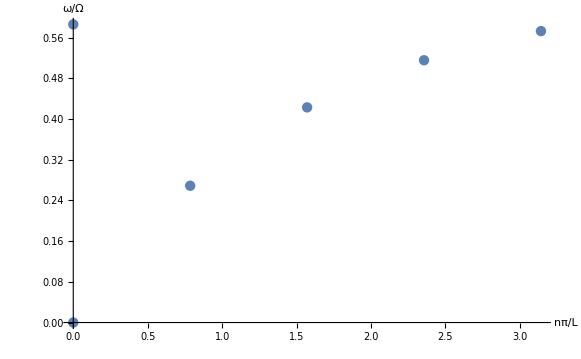

```mathematica
k = Table[(λlist[[Ordering[Abs[Eigenvectors[Pm . Lm][[i]]],-1]]][[1]][[1]] Pi)/L,{i,1,n}]
data=Transpose@{k,Sqrt[Eigenvalues[Pm.Lm]]};
ListPlot[data, AxesLabel->{"nπ/L", "ω/Ω"}]
```

```mathematica
λlist[[Ordering[Abs[Eigenvectors[Pm . Lm][[n-10]]], -1]]][[1]][[1]]
```

2

```mathematica
λlist[[3]][[1]]
```

2

```mathematica
N[Pm]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-9.8696,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-9.8696,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-19.7392,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-39.4784,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-39.4784,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-49.348,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-49.348,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-78.9568,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-88.8264,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-88.8264,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-98.696}}

```mathematica
{57.43100298022997,40.1863068099706,40.18630680817287,24.943006142592903,24.943006142592903,17.316063441018624,17.316063441018624,16.047675783965182,16.04767578396518,14.137228705348134,13.631614327527885,13.631614327527885,6.768406854380646,6.768406854380645,5.081772225147757,3.9276784331511334,3.9276784331511325,0.}
```

{57.431,40.1863,40.1863,24.943,24.943,17.3161,17.3161,16.0477,16.0477,14.1372,13.6316,13.6316,6.76841,6.76841,5.08177,3.92768,3.92768,0.}

```mathematica
NIntegrate[Abs[Cos[π(x-1/2)]]/Abs[x]^2, {x,-0.5,0.5}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {7.82632×10^-58}. NIntegrate obtained 1.63115×10^228 and 1.60779×10^228 for the integral and error estimates.

1.63115×10^228

```mathematica
Eigenvectors[Pm . Lm]
```

{{0,4.58260089292494×10^-7,0.000869088636359603,-0.000029333005681541,0.0030128595194413,-0.0002212655159422,-2.52736147638069×10^-6,-0.000145111885699045,1.6719914232094×10^-6,-0.000298404607794087,0.00658343546882564,0.0000300640046199147,-0.0000120432234516609,0.00765414497025703,-0.000141327833123456,0.0250196824483865,0.00167011817151057,0.000593925689203515,-0.000669023125740444,0.999629173597396},{0,0.000999713059416797,-3.91363385792772×10^-6,0.00749163557952174,-0.0000223210086484645,0.000776045528459596,0.0297565767171219,0.0000712879227265817,0.000385584967652184,-0.0000206048497646995,0.000138379096470866,0.000815485238410154,0.0576318004860898,0.00027653740033425,-0.00100199587113463,0.0000755515209010872,-0.000684038064818335,-0.997674520590659,-0.0194448947336866,0.000670466800409977},{0,-0.000119729761799793,0.0000321456732546767,-0.00128873917031292,0.000121772632754783,-0.0412837119489027,-0.00295409680654741,0.0000604289082863408,-0.0189923092932425,-0.0000406825318195078,0.00053020861485752,-0.0329592557413563,0.0770264065267061,0.000922604195994575,-0.0737750085093979,-0.00872606683698321,-0.00126160826747184,0.0277565661205829,0.992276658129374,-0.000362083184882638},{0,-0.0000164376436884324,-0.00306333542411567,-7.23617970789422×10^-6,-0.0126119083172325,-0.000435515204255018,-0.0000796320029057108,-0.0206463399241795,-0.00011303007830375,-0.0310718707403559,-0.0397057619190301,-0.000419405556542351,0.00270023981115907,-0.0371352637286195,-0.00193582379173147,0.772255116671638,0.630905350571114,0.000743683207144972,0.0112360570079785,-0.0304383890809022},{0,-1.39831202023871×10^-6,-0.00239258651090507,-0.0000486301475166516,-0.0105132731942037,-0.000188200463945576,-0.000267200015021729,0.0269477292127787,0.0000268330187755117,0.0459054823145093,-0.0357089544676015,-0.000123044981769747,0.00151306157041685,0.0581206465059634,-0.00202885789445123,0.576347846017556,-0.812214424677465,0.000224037238801065,0.00490433330646291,-0.0223017850830641},{0,0.000694807594992582,0.0000318075418689733,0.00720976980620374,0.0000675928144812022,0.0364217095988413,0.0173873699907509,-0.000781224463217855,0.0777623154943258,-0.000263157951281864,-0.000445666071519619,0.0906293488335347,-0.37160273641851,0.00428615031959804,-0.909177175288134,0.0000442610444925369,0.00039989019486329,-0.0322961097534639,-0.135290236576805,-0.000620483903044843},{0,-0.00168546880035357,-0.0000169375447846247,-0.0170342540175034,-0.0000121994860183795,-0.0239347199738225,-0.0430842113699722,0.000635336426818136,-0.0382973528325983,0.000193749743356133,-0.0000758306914149608,-0.0477665655925291,0.893842712368968,-0.00113012493763746,0.40155606487775,0.000487148987017869,0.000554323376298291,0.0814210745660484,0.163388522426617,-0.0000615238706859224},{0,6.03867969560436×10^-6,0.0000219571389863789,0.000057287827359044,0.00145788865620394,-0.000680503129075204,0.000117723130809102,-0.066217967678795,-0.000142292131279293,-0.131990574985549,-0.00298177143001325,-0.00143037821554953,-0.00179413339270606,0.985947107367276,0.00710840122424314,-0.00706100823601754,0.0758703774023657,-0.000542216655088245,0.00131707945607107,-0.015048521139709},{0,-8.28932946290819×10^-6,0.0121439988700692,-0.000113261862854173,0.0529791784964707,-0.00125614689047753,-0.000525891887439621,0.000751401250672197,-0.000989147328233998,-0.00334813025681516,-0.993977240779464,0.000907911705882941,0.00430672192702021,-0.00449257126374802,0.0000613339182593911,-0.0922687998548389,0.00887670275663701,-0.000128158393328415,-0.000709601016331609,0.0201977236463253},{0,-0.0000261624941676265,0.0000182619011636259,-0.00359979250734174,-0.000402435965640357,0.131341310065042,0.000904502448639084,-0.000166206895307706,0.182653107636825,0.00053765971243107,-0.000234028306990571,-0.968869020090542,0.0039702683272875,-0.000835294590089486,-0.0908805775154011,-0.000166529655753511,-0.000283726366715583,0.000243636024553292,-0.0488865238236477,0.000115992993420907},{0,7.98935158498909×10^-6,0.000422957120853604,4.54348168718397×10^-6,-0.0143984948510336,0.000480998731678481,0.000408111451508591,-0.334641456029289,-0.00037153958461319,0.928103749967651,-0.00582216695783143,0.000852789208454376,-0.000616781343042111,0.134719169923476,0.000774116662965478,-0.00624960591051231,0.0905813176486978,0.0000130712100691566,-0.0000119053658044277,-0.00126543398862827},{0,-8.99595661448857×10^-6,0.0000961827813185316,0.000106562588836386,-0.000105236032176203,-0.758289937959878,-0.00453589072723223,-0.00120436786825011,0.646224417399802,0.00340047164561513,-0.00108477098329249,0.00103869603829285,0.0045315960612397,0.00137405659925091,0.0515360136908966,0.0000521668193268063,0.000390501769658646,-0.000249647895861306,-0.0683760871625479,-0.000778470890931761},{0,-0.00481070948897273,0.0000496576223953426,-0.0532878584155175,-0.00101974275262166,0.00185630466384325,0.99007811499292,-0.000371558912925289,-0.00163211527767118,0.000136646507199195,0.000146496962472981,-0.00400078896643117,0.0829926531197868,0.000141159707036317,0.000301271948783795,-0.0000582816349697671,0.000993556377870812,0.0997058590954684,0.00539521186429251,0.0000505821315765076},{0,0.0000545418171853819,-0.000111761093525441,0.00251059980099075,-0.000124080691767841,0.544332687799942,-0.000815742938565656,0.00583726883866716,0.736323826213822,0.00357336809213192,0.00108598401353959,0.300006452559145,-0.008632911293236,0.0028410702064605,0.208666599807452,0.000107610693950132,0.00130377585298117,-0.000729588006598541,0.166863528560386,0.000474701276736658},{0,0.0000366383654200889,-0.000387377328726282,0.0000245637887562146,0.00923274533717662,0.000278293149323062,0.0000507057797480923,-0.888128588460476,0.000224569018765369,-0.393718405289883,0.0018143305499136,0.000364155633709529,-0.000562142061349946,-0.184513342473842,0.000617708180863678,0.0105960586009885,-0.148203240723275,-0.000125794095730028,-0.000103462710555457,0.001450028384244},{0,-0.000114069295097092,-0.038108326365984,-0.0028656511296339,0.989223266222008,0.000184432735680377,0.00259869340057922,0.00479212136381069,0.00057444879313517,0.0305134057712904,0.109884648550276,0.000263723995680169,0.0281495628836167,0.00419569827268151,0.000312167154613432,0.074880706939092,-0.00045393742885902,0.00114932441775822,0.00169337285977612,-0.0227901499753652},{0,-0.0227305095146598,-0.0000409837077154337,0.980379551410896,-0.000186718126439707,0.00237632789862511,0.136449407782427,-0.0000287902865928213,0.00268851183935292,0.0000626108204747737,-0.000026150408263162,0.0197204079023849,0.107450422730152,-9.9218733444368×10^-6,0.00159475938614661,0.0000815366314144533,0.000467436127750666,0.0879304307310932,0.00622867276356562,-0.000296438305136906},{0,0.000105181829770065,-0.978369708032406,-0.000124004596068681,-0.143153120497509,-0.000659323594983767,-0.000166633199819258,0.000239135952173837,-0.000238224055825835,-0.00141452339655671,-0.120102411636844,0.0000176466854512161,-0.00252003071527523,-0.000205330699082734,-0.000594290497656814,-0.0836110240346497,0.00285582240946211,-0.000189935158865543,-0.000468577621933935,0.0294405261074617},{0,-0.958569137922159,0.000601177724125001,-0.189751873017345,0.0000574777839318524,-0.00101096919581906,-0.136308963932801,0.00093886129384465,-0.00059503893455307,0.000133293738060743,0.0000733198893535319,-0.00432958706228072,-0.115318760371891,0.000117842520324085,-0.000471220012731733,-0.000560671957704257,0.00052197034603753,-0.114910798947263,-0.00584388459704836,0.00016777431456447},{0.929746603353914,0.0000853181041848147,0.17452414009071,0.000118327972443917,0.123031335741857,0.000065031428943432,0.0000167342369975667,0.000287289882684129,-0.000586083824429936,0.000983307517968364,0.0978691850001394,-0.0000566728440157167,0.00195620248859486,-0.00179983925245239,-0.000468332183758333,0.122738213915369,-0.00364087788037372,0.0000633329509633344,0.000215388758292986,0.25555979372863}}

```mathematica
λlist
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{0,1},{5,0},{1,1},{2,1},{3,1},{6,0},{4,1},{7,0},{5,1},{6,1},{8,0},{7,1},{9,0},{8,1},{0,2}}

```mathematica
Sqrt[Eigenvalues[Pm.Lm]]
```

{2.61776783671463,2.40733496162356,2.31046499353654,2.21640947385688,2.15292648639312,2.04068292019557,2.03624754355255,1.88445493802792,1.82393450934344,1.77831296471007,1.67940392574924,1.63657174704501,1.60347675657741,1.51895896173134,1.49979832726157,1.38301035784715,1.12716971643387,0.830242733425732,0.465876678811519,0}

```mathematica
Eigenvectors[Pm.Lm][[12]]
```

{0,-8.99595661448857×10^-6,0.0000961827813185316,0.000106562588836386,-0.000105236032176203,-0.758289937959878,-0.00453589072723223,-0.00120436786825011,0.646224417399802,0.00340047164561513,-0.00108477098329249,0.00103869603829285,0.0045315960612397,0.00137405659925091,0.0515360136908966,0.0000521668193268063,0.000390501769658646,-0.000249647895861306,-0.0683760871625479,-0.000778470890931761}

```mathematica
Export["Rechthoek_PmLm_L5n25_15-12-19.csv", Pm.Lm,"CSV"]
```

Rechthoek_PmLm_L5n25_15-12-19.csv

```mathematica
Eigenvectors[Pm.Lm][[50]]
```

{0.404136282478391,-0.0000741282826080657,0.071293938795187,-0.000128034483432515,0.000287264748835,0.0441803686422345,0.000489364095133422,0.000263316082651467,0.00400328758356214,-0.0000818969111512796,-0.000120864270509626,0.0327465069589824,0.0638432213032745,-0.0000760345196781015,0.000932465417233262,0.120570548892941,0.0316706660923509,-0.00045289212791182,0.000995752823933819,0.011323121528643,-0.000265538854267829,-0.00100337069005907,0.000568341948549597,0.000173022334455015,-0.000276510655591778,0.00555877504898276,0.00366137951713669,-0.586624556843457,-0.000445384451971421,0.0000814950846502618,0.000317486955813475,0.00461014859855832,0.00170038566125951,0.000189578524881391,0.0174699291618398,0.0268299215141346,0.000463789296879876,0.000537069809529718,0.0298913274943127,-0.0000730001272963561,0.000501086459602118,-0.0597116321338624,0.676386550766561,0.000235206771491947,0.0000431923151556941,-0.0016672807602787,0.000789837196549182,0.0267045155606975,0.0298801791363934,0.00349047306219183}

```mathematica
Eigenvalues[Pm.Lm][[50]]
```

0

```mathematica
Export["Dispersie_L4_n50", data, "CSV"]
```

Dispersie_L4_n50

```mathematica
data
```

{{(5 π)/4,4.30516989884586},{2 π,3.4775501772543},{(7 π)/4,3.44781560578627},{(7 π)/2,3.44263205987334},{(11 π)/4,3.38967851455731},{(3 π)/2,3.34143870228118},{0,3.28128934994144},{(13 π)/4,3.27344414565799},{(13 π)/4,3.25276922481146},{(5 π)/2,3.20368829124362},{3 π,3.19135536812102},{(3 π)/4,3.19042279849413},{π,3.18538478496549},{3 π,3.13763483011257},{(9 π)/4,3.12525222952747},{π/4,3.05199616863535},{π/2,3.01647791425736},{(11 π)/4,2.95992946508301},{2 π,2.94607058390598},{(7 π)/4,2.932186966929},{(11 π)/4,2.90239606737926},{(5 π)/2,2.82553420498202},{(3 π)/2,2.82493907178389},{(5 π)/4,2.70806342786732},{(9 π)/4,2.67975095835052},{π,2.62164445140116},{(9 π)/4,2.59472325501142},{(3 π)/4,2.57247737208596},{0,2.55368404352637},{2 π,2.48180513859836},{2 π,2.42868910935857},{π/2,2.37588891235819},{π/4,2.36368464484789},{(7 π)/4,2.33917707224697},{(7 π)/4,2.22571044996082},{(3 π)/2,2.14463837559707},{(5 π)/4,2.03528801249627},{(3 π)/2,2.01768926209377},{π,1.85684254054227},{(5 π)/4,1.79909539776056},{(3 π)/4,1.71418807852522},{π/2,1.61858180519907},{π,1.55896173232162},{0,1.48344716909474},{π/4,1.47152778279964},{(3 π)/4,1.27600898605107},{π/2,0.953759092694953},{π/4,0.539970995579004},{(5 π)/4,0.506154978422971 ⅈ},{(5 π)/4,0}}